# NFL Players Heights VS Weights VS Position

## Load Data

```mathematica
SetDirectory[NotebookDirectory[]];
rawData=Import["NFL.csv"];
{header,data}={rawData[[1]],rawData[[2;;All]]};
```

```mathematica
position=Position[header,"Position"][[1,1]];
weight=Position[header,"Weight (lbs)"][[1,1]];
height=Position[header,"Height (inches)"][[1,1]];
```

```mathematica
Grid[{Range[header//Length],header}//Transpose]
```

1 | Age
2 | Birth Place
3 | Birthday
4 | College
5 | Current Status
6 | Current Team
7 | Experience
8 | Height (inches)
9 | High School
10 | High School Location
11 | Name
12 | Number
13 | Player Id
14 | Position
15 | Weight (lbs)
16 | Years Played

```mathematica
positionsID=((data[[All,position]]//DeleteDuplicates)//Sort)[[2;;All]]
```

{C,CB,DB,DE,DL,DT,FB,FS,G,ILB,K,LB,LS,MLB,NT,OG,OL,OLB,OT,P,QB,RB,SAF,SS,T,TE,WR}

## Initial Draft

```mathematica
positions=data[[All,position]];
weights=data[[All,weight]]*0.453592;
heights=data[[All,height]]*0.0254;
```

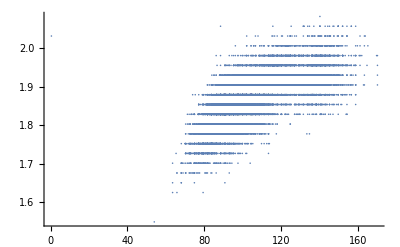

```mathematica
ListPlot[{weights,heights}//Transpose]
```

## Trying transposing the data

```mathematica
triplets=Transpose[{heights,weights,positions}];
filtered=Cases[triplets,{a_,b_,c_}/;StringLength[c]≥1];
```

```mathematica
clustered=Map[Cases[filtered,{a_,b_,#}->{a,b}]&,positionsID];
clustered[[1]]
```

{{1.905,140.16},{1.9558,138.799},{1.9304,137.892},{1.9304,139.253},{1.8796,136.078},{1.905,131.995},{1.905,145.603},{1.905,139.706},{1.905,138.346},{1.9558,146.964},{1.9304,140.614},{1.905,136.985},{1.9304,139.706},{1.9304,138.799},{1.905,137.438},{1.9304,136.078},{1.905,131.995},{1.9558,151.5},{1.9304,139.253},{1.9304,138.799},{1.905,136.078},{1.8542,139.253},{1.905,122.016},{1.9304,141.067},{1.905,142.881},{1.9558,142.881},{1.9558,137.892},{1.9304,134.263},{1.905,136.531},{1.905,132.449},{1.9304,140.614},{1.905,133.81},{1.9558,139.253},{1.9558,142.881},{1.9558,138.346},{1.905,140.16},{1.9304,138.346},{1.905,139.706},{1.905,131.995},{1.9558,135.17},{1.8796,134.263},{1.8796,136.078},{1.905,136.078},{1.8796,129.274},{1.905,136.078},{1.9304,151.953},{1.8796,136.078},{1.905,136.078},{1.9304,136.078},{1.8796,135.624},{1.8796,135.17},{1.9304,144.242},{1.9304,142.881},{1.9304,135.624},{1.905,139.706},{1.8542,141.067},{1.905,133.81},{1.9304,135.624},{1.9304,141.067},{1.905,136.985},{1.9558,111.13},{1.8542,108.862},{1.9558,145.149},{1.8796,137.438},{1.8542,138.346},{1.9304,137.892},{1.9558,139.706},{1.9304,140.614},{1.9304,128.82},{1.9812,141.974},{1.9304,133.356},{1.9558,141.974},{1.9558,140.16},{1.9812,140.16},{1.9558,135.624},{1.9812,138.346},{1.8796,138.346},{1.9304,140.614},{1.905,144.242},{1.9304,141.974},{1.9812,139.253},{1.9558,134.717},{1.9304,134.717},{1.905,131.542},{1.905,139.253},{1.905,141.974},{1.9558,125.191},{1.9812,142.881},{1.905,133.81},{1.9558,138.346},{1.905,135.17},{1.9304,131.088}}

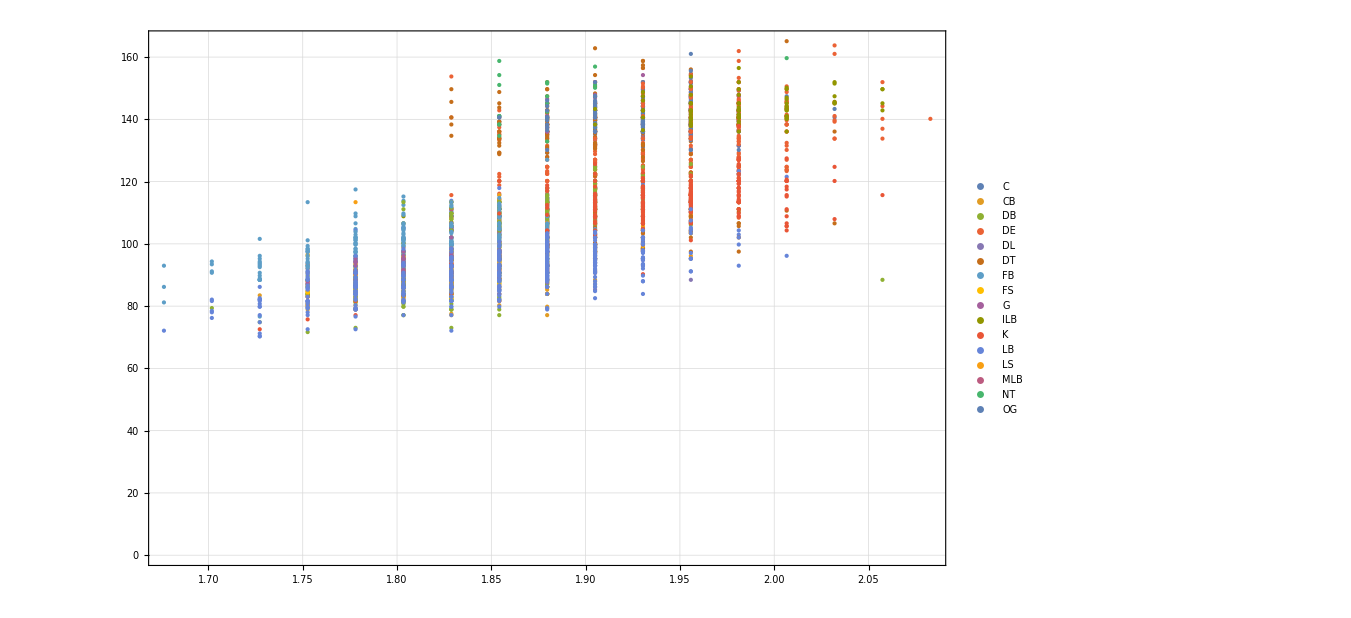

```mathematica
clustered=Map[Cases[filtered,{a_,b_,#}->{a,b}]&,positionsID];
ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotStyle->Directive[PointSize[Large],Opacity[1]]
,PlotLegends->positionsID
]
```

## Manual Clustering of Positions

```mathematica
clusteredIDs={{"C","LS","OG","OT","NT","T","G","OL","DL","DT","DE"},{"DB","CB","OLB","SAF","SS","FS"},{"K","P"},{"ILB","LB","MLB"},{"QB"},{"RB","FB"},{"TE"},{"WR"}}
```

{{C,LS,OG,OT,NT,T,G,OL,DL,DT,DE},{DB,CB,OLB,SAF,SS,FS},{K,P},{ILB,LB,MLB},{QB},{RB,FB},{TE},{WR}}

```mathematica
clusteredIDs//Length
```

8

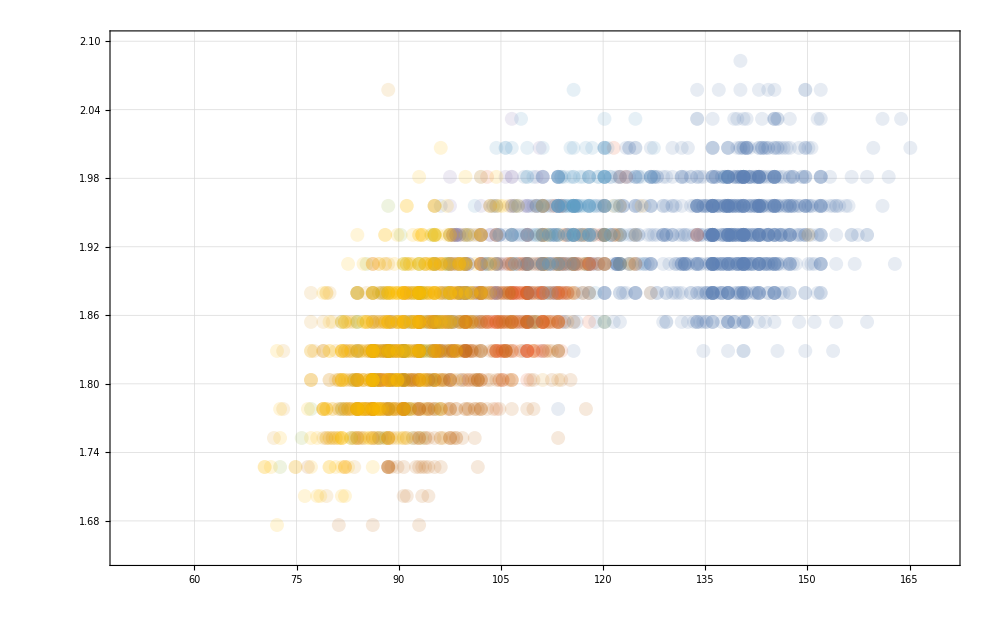

```mathematica
clustered=Map[Cases[filtered,{a_,b_,c_}/;MemberQ[#,c]->{b,a+RandomReal[{-0,0}]}]&,clusteredIDs];
base=ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,ColorFunction->"BrightBands"
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotRange->{{50,170},{1.65,2.1}}
,PlotLegends->{"Line","DB","K","LB","QB","RB","TE","WR"}
,PlotStyle->Directive[PointSize[.01],Opacity[.15]]
]
```

## Highlighting a cluster

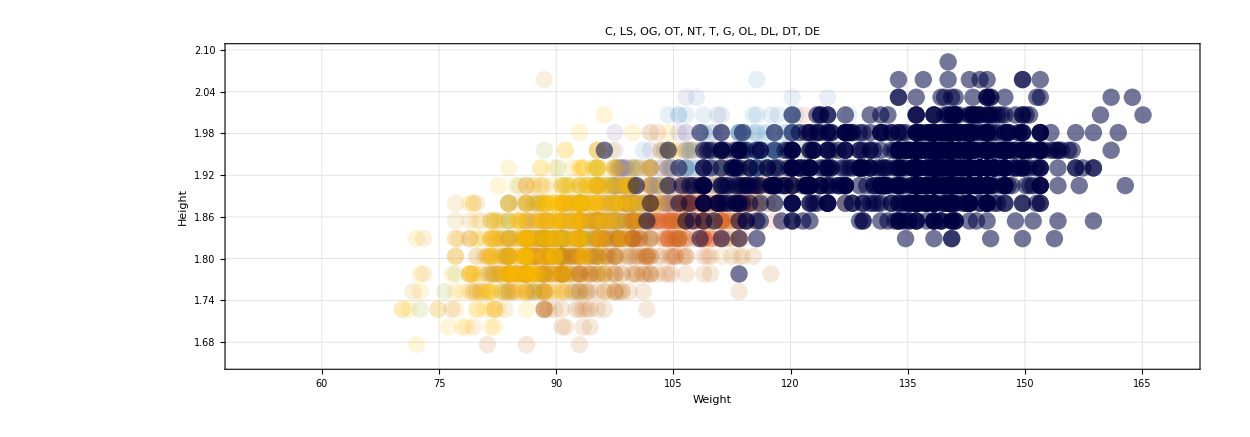

```mathematica
index=1;
clustered=Map[Cases[filtered,{a_,b_,c_}/;MemberQ[#,c]->{b,a}]&,{clusteredIDs[[index]]}];
layer=ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotRange->{{50,170},{1.6,2.1}}
,PlotStyle->Directive[PointSize[.01],Darker[Blue,.75],Opacity[.5]]
];
Show[base,layer
,AspectRatio->.35
,FrameLabel->(Style[#,40]&/@{"Weight","Height"})
,ImageSize->1250
,PlotLabel->(StringDelete[ToString[clusteredIDs[[index]]],{"{","}"}]//Style[#,50]&)
]
```

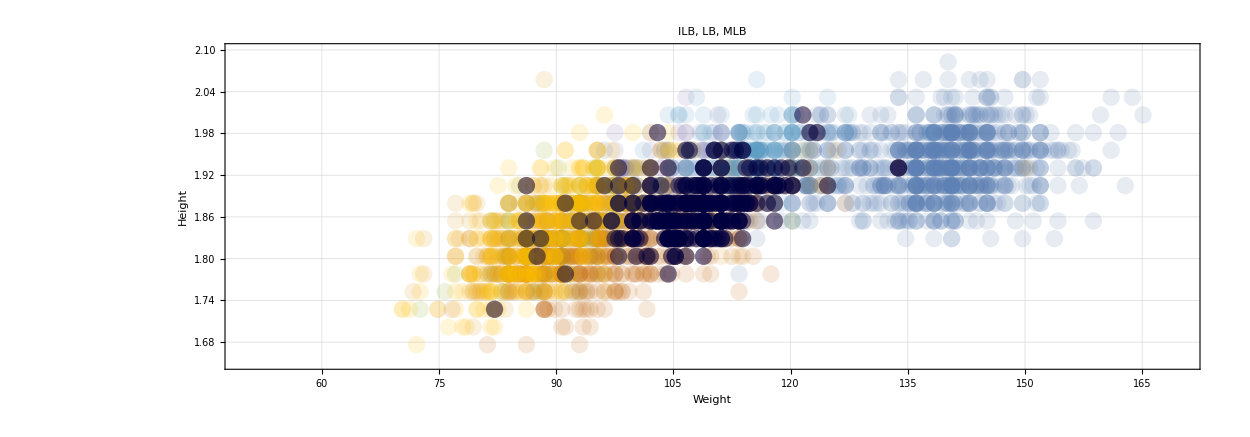

```mathematica
index=4;
clustered=Map[Cases[filtered,{a_,b_,c_}/;MemberQ[#,c]->{b,a}]&,{clusteredIDs[[index]]}];
layer=ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotRange->{{50,170},{1.6,2.1}}
,PlotStyle->Directive[PointSize[.01],Darker[Blue,.75],Opacity[.5]]
];
Show[base,layer
,AspectRatio->.35
,FrameLabel->(Style[#,40]&/@{"Weight","Height"})
,ImageSize->1250
,PlotLabel->(StringDelete[ToString[clusteredIDs[[index]]],{"{","}"}]//Style[#,50]&)
]
```

## Improving Aesthetics

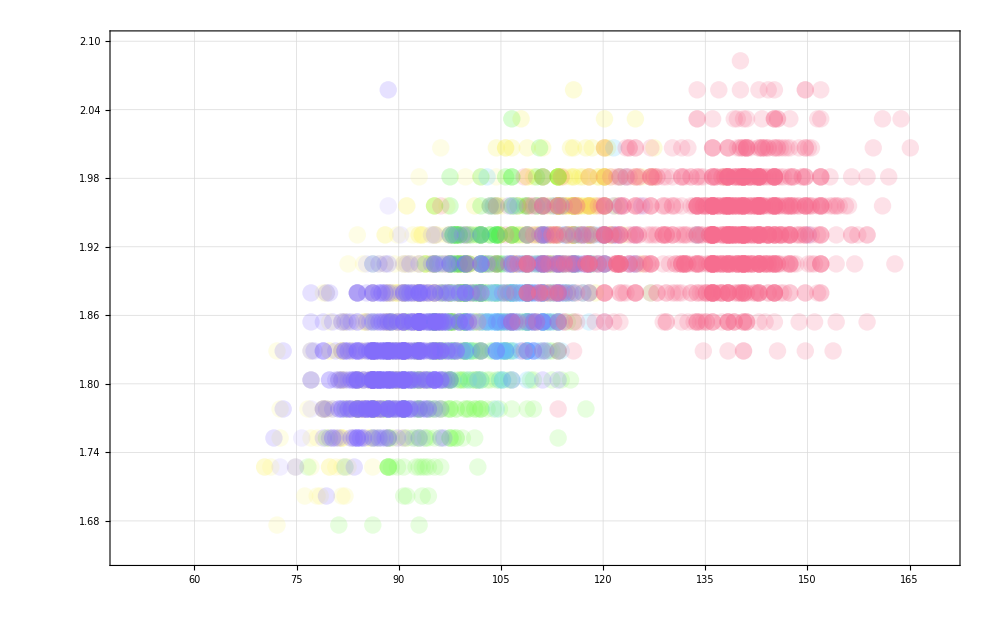

```mathematica
clustered=Map[Cases[filtered,{a_,b_,c_}/;MemberQ[#,c]->{b,a+RandomReal[{-0,0}]}]&,clusteredIDs];
colors=ColorData["BrightBands"][#/10]&/@Range[clusteredIDs//Length];
base=Table[ListPlot[clustered[[i]]
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotRange->{{50,170},{1.65,2.1}}
,PlotStyle->Directive[colors[[i]],PointSize[.0125],Opacity[.2]]
]
,{i,1,clustered//Length}]//Reverse//Show
```

## Putting it all together

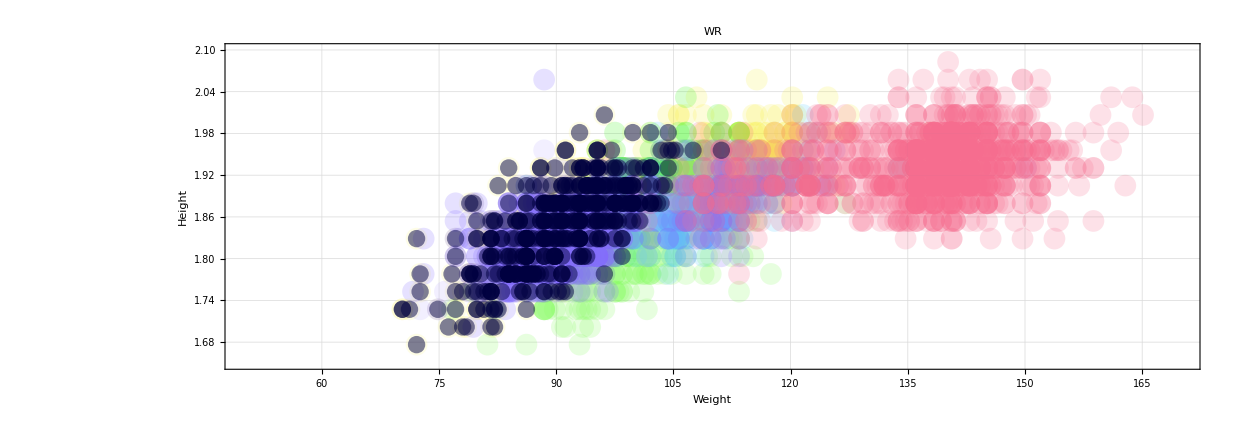
-Graphics- |

NFL08.png

```mathematica
index=8;
clustered=Map[Cases[filtered,{a_,b_,c_}/;MemberQ[#,c]->{b,a}]&,{clusteredIDs[[index]]}];
layer=ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotRange->{{50,170},{1.6,2.1}}
,PlotStyle->Directive[PointSize[.01],Darker[Blue,.75],Opacity[.5]]
];
swatch=SwatchLegend[colors,{"Line","DB","K","LB","QB","RB","TE","WR"},LegendMarkerSize->30,LabelStyle->20];
grid=Grid[{{
Show[base,layer
,AspectRatio->.35
,FrameLabel->(Style[#,40]&/@{"Weight","Height"})
,ImageSize->1250
,PlotLabel->(StringDelete[ToString[clusteredIDs[[index]]],{"{","}"}]//Style[#,50]&)
]
,
swatch
}}]
Export["NFL0"<>ToString[index]<>".png",grid,ImageSize->2500,ImageResolution->300]
```